# General

## Configuration

```mathematica
Off[General::munfl];
```

## Values

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

### Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

### Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

### Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

# Raw Data

```mathematica
(*(*DUC only - 0 ns OSC delay*)
dataDJ={
{00.00,Mean[{2,2,2,3}]},
{00.01,Mean[{-3,-3,0,-2}]},
{00.02,-Mean[{3,3,5,5}]},
{00.03,-Mean[{8,7,10,10}]},
{00.04,-Mean[{12,12,12,14}]},
{00.05,-Mean[{17,15,17,15}]},
{00.06,-Mean[{19,19,20,17}]},
{00.07,-Mean[{20,20,20,22}]}
};*)
```

```mathematica
(*(*DUC only - -935.02 ns OSC delay*)
dataDJ={
{00.00,Mean[{0,2,2,1}]},
{00.50,Mean[{8,8,8,6}]},
{01.00,Mean[{14,15,14,14}]},
{01.50,Mean[{22,19,20,20}]},
{02.00,Mean[{27,28,27,25}]},
{02.50,Mean[{33,34,33,34}]},
{03.00,Mean[{39,41,39,41}]},
{03.50,Mean[{47,46,47,46}]}
};*)
```

```mathematica
(*(*DUC only - -934.98 ns OSC delay*)
dataDJ={
{-5.00,Mean[{-65,-65,-65,-62}]},
{-4.00,-Mean[{52,51,52,53}]},
{-3.00,-Mean[{39,39,36,41}]},
{-2.00,-Mean[{25,25,24,24}]},
{-1.00,-Mean[{14,13,10,11}]},
{00.00,Mean[{1,0,1,1}]},
{01.00,Mean[{13,14,15,14}]},
{02.00,Mean[{28,27,27,27}]},
{03.00,Mean[{41,42,41,40}]},
{04.00,Mean[{55,53,52,52}]},
{05.00,Mean[{66,65,66,66}]}
};*)
```

```mathematica
(*(*DUC only - -898.6479 ns OSC delay*)
dataDJ={
{-5.00,Mean[{1,1,4,3,0}]},
{-4.00,Mean[{1,3,0,1,3}]},
{-3.00,Mean[{0,1,1,1,-1}]},
{-2.00,Mean[{3,1,-1,3,3}]},
{-1.00,Mean[{3,0,4,3,2}]},
{00.00,Mean[{2,2,-1,2,1}]},
{01.00,Mean[{0,0,1,0}]},
{02.00,Mean[{1,1,1,3}]},
{03.00,Mean[{-1,1,0,1,1}]},
{04.00,Mean[{1,0,1,2,-1}]},
{05.00,Mean[{2,0,1,1,0}]}
};*)
```

```mathematica
(*(*DUC only - 0 ns OSC delay*)
dataDJ={
{00.00,Mean[{0,0,0}]},
{00.01,-Mean[{50,50,46}]},
{00.02,-Mean[{102,102,99}]},
{00.03,-Mean[{154,153,150}]}
};*)
```

```mathematica
(*(*DUC only - 0 ns OSC delay*)
dataDJ={
{00.000,0.},
{00.001,-4.},
{00.002,-10},
{00.003,-13}
};*)
```

```mathematica
(*(*DUC only - -12500.1 ns OSC delay*)
dataDJ={
{00.000,0.},
{00.010,-4.},
{00.020,-12},
{00.030,-16},
{00.040,-27},
{00.050,-34},
{00.060,-37}
};*)
```

```mathematica
(*DUC only - 0. ns OSC delay*)
dataDJ={
{00.000,0.},
{00.050,15.},
{00.100,22.},
{00.150,36.},
{00.200,48.},
{00.250,59},
{00.300,73}
};
```

```mathematica
(*DUC only - 660.714 ns OSC delay*)
dataDJ={
{-5.00,Mean[{-3,-4,-3,-3}]},
{-4.00,Mean[{-1,-3,-3,-3,-4}]},
{-3.00,Mean[{-1,0,-1,-1,-4}]},
{-2.00,Mean[{0,-1,-3,1,-3}]},
{-1.00,Mean[{0,0,0,1,1}]},
{00.00,Mean[{3,1,1,3,1}]},
{01.00,Mean[{3,1,1,3,3}]},
{02.00,Mean[{4,3,1,5,0}]},
{03.00,Mean[{4,4,4,5,3}]},
{04.00,Mean[{4,5,4,4,4}]},
{05.00,Mean[{5,3,6,6,6}]}
};
```

```mathematica
dataDJ[[;;,1]]*=1.*^0;
dataDJ[[;;,2]]/=360.;
```

# Process

## Fit

```mathematica
(*linear model fit*)
fitRes=LinearModelFit[
dataDJ,
{1.,t},
t
];
```

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot Data

```mathematica
(*plot raw data*)
plotRawData=ListPlot[
{
dataDJ
},
PlotRange->{Full,{Full,Full}},
FrameLabel->{ 
{Style["Urukul-Phaser ϕ_Relative (turns)",{Black,Directive[15]}],None},
{
Style["Frequency (MHz)",{Black,Directive[15]}],
Style["DUC Delay",{Black,Directive[15]}]
}
},
Joined->False,
PlotStyle->{{Red},{Blue}}
];
```

```mathematica
(*plot fitted data*)
plotFitData=Plot[
fitRes[t],
{t,dataDJ[[1,1]],dataDJ[[-1,1]]}
];
```

# Show

| Estimate | Standard Error | Confidence Interval
1. | 0.00296717 | 0.000331641 | {0.00221695,0.0037174}
t | 0.00242045 | 0.000104874 | {0.00218321,0.0026577}

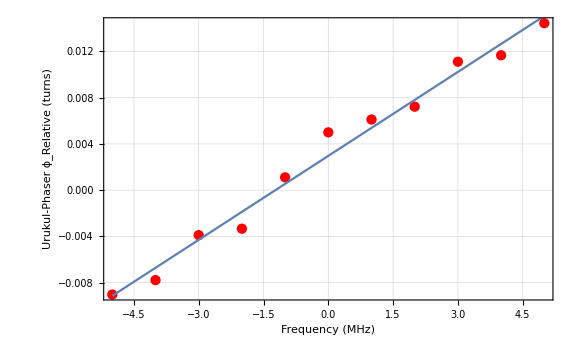

```mathematica
fitParams
Show[
plotRawData,
plotFitData
]
```